# Demonstrating the use of SimpleGroup.m using SU(N) algebras

B Ananthanarayan, Souvik Bera, Subhasish Chakrabarty, Souradeep Das, Amitabha Lahiri, Suhas Sheikh, Sarthak Talukdar

SimpleGroup is a Mathematica package that produces graphical outputs for Lie Algebra representations, including weight diagrams and Dynkin diagrams. Additionally, it can generate the Cartan Matrix, Clebsch-Gordan coefficients, as well as use several notations such as canonical and weight-space realization of vectors. We demonstrate the usage of this package using some well-known properties of the most common SU(N) algebras.

```mathematica
<<SimpleGroup.m
```

Package SimpleGroups (v.0.98β (date:06.05.10)) is loaded

Use SetGroup[] to set the group to work with.

## Lie Algebra SU(2): Angular Momentum Algebra

We will begin with the angular momentum algebra or the SU(2) group. We will verify some basic properties to show that the commands in this package make sense.

```mathematica
SetGroup[SU[2]]
```

Set group is  A(1)

Rank of the group = 1

First, we define a few common representations of the algebra: say the vector representation 3 and the spinor representation 2. To define them we use the BuildRep function with the argument as the largest Dynkin label (which here is twice the azimuthal quantum number ).

The outputs that we obtain are the Dynkin Labels of each of the weight vectors, followed by their multiplicity, which is 1 for each weight in the simple example of SU(2).

```mathematica
VectorRep=BuildRep[{2}]
```

{{{-2},1},{{0},1},{{2},1}}

```mathematica
SpinorRep=BuildRep[{1}]
```

{{{-1},1},{{1},1}}

Then we demonstrate how the tensor product of the two representations decomposes as a tensorial sum, following the well-known addition rules of angular momentum algebra.

```mathematica
CGDecomposition[ SpinorRep, VectorRep]
```

2 ⊗ 3 = 4 ⊕ 2

{{3},{1}}

The package also allows one to obtain the Clebsch-Gordan coefficients for decomposing a tensor product into a tensor sum. Here as arguments of the function, we insert the Dynkin Labels of the representations getting added. It returns the decomposition as well as the CG coefficients.

```mathematica
CGCoefficients[{1}, {2}]
```

2 ⊗ 3 = 4 ⊕ 2

({1,0}
{0}) | ({1,0}
{0}) | ({1,0}
{1})
({2,0}
{0}) |  | √(2/3)
({2,0}
{1}) | -1/(√3) | ({1,0}
{1}) | ({1,0}
{0}) | ({1,0}
{1})
({2,0}
{1}) |  | 1/(√3)
({2,0}
{2}) | -√(2/3) | Representation   {1}
    ({3,0}
{0}) | ({1,0}
{0})
({2,0}
{0}) | 1({3,0}
{1}) | ({1,0}
{0}) | ({1,0}
{1})
({2,0}
{0}) |  | 1/(√3)
({2,0}
{1}) | √(2/3) | ({3,0}
{2}) | ({1,0}
{0}) | ({1,0}
{1})
({2,0}
{1}) |  | √(2/3)
({2,0}
{2}) | 1/(√3) | ({3,0}
{3}) | ({1,0}
{1})
({2,0}
{2}) | 1Representation   {3}

## Lie Algebra SU(3)

We will next look at the higher dimensional Lie Algebra SU(3) or A(2). Being a higher-ranked algebra, this has the added feature of weight diagrams which can be conveniently plotted using the package.

```mathematica
SetGroup[SU[3]]
```

Set group is  A(2)

Rank of the group = 2

The package SimpleGroup.m has the advantage of being beautiful with graphics. Here we look at the affine Dynkin diagram of SU(3) or A(2):

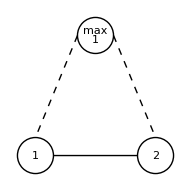

```mathematica
DynkinDiagram
```

```mathematica
CartanMatrix[SimpleRoots]//MatrixForm
```

(2 | -1
-1 | 2)

This command will return the list of all simple roots of the algebra (in weight space). The first sub-list consists of all positive roots and the second negative roots. The next command returns the fundamental weights in the weight space.

```mathematica
rs=RootSystem[SimpleRoots]
```

{{{1,-1,0},{0,1,-1},{1,0,-1}},{{-1,0,1},{-1,1,0},{0,-1,1}}}

```mathematica
fw=FundamentalWeight[SimpleRoots]
```

{{2/3,-1/3,-1/3},{1/3,1/3,-2/3}}

We will the build two representations and look at their weight diagrams. Note here that the argument of the BuildRep function is a two-dimensional vector since the rank of the algebra is 2. The blue lines in the weight diagram indicate the fundamental weights, and the numerical labels indicate multiplicities.

```mathematica
rep1=BuildRep[{1,2}, OutputMethod->"Weights"]
```

{{{-5/3,1/3,4/3},1},{{-2/3,-2/3,4/3},1},{{1/3,-5/3,4/3},1},{{-2/3,1/3,1/3},2},{{1/3,-2/3,1/3},2},{{1/3,1/3,-2/3},2},{{-5/3,4/3,1/3},1},{{4/3,-5/3,1/3},1},{{-2/3,4/3,-2/3},1},{{4/3,-2/3,-2/3},1},{{1/3,4/3,-5/3},1},{{4/3,1/3,-5/3},1}}

The previous notation had outputs in the canonical realization. We can view them in the form of Dynkin labels:

```mathematica
DynkinLabels[rep1]
```

{{{-2,-1},1},{{0,-2},1},{{2,-3},1},{{-1,0},2},{{1,-1},2},{{0,1},2},{{-3,1},1},{{3,-2},1},{{-2,2},1},{{2,0},1},{{-1,3},1},{{1,2},1}}

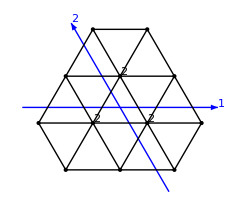

```mathematica
PlotRep2D[rep1, SimpleRoots]
```

```mathematica
rep2=BuildRep[{2,0}, OutputMethod->"Weights"];
```

```mathematica
DynkinLabels[rep2]
```

{{{0,-2},1},{{-1,0},1},{{1,-1},1},{{-2,2},1},{{0,1},1},{{2,0},1}}

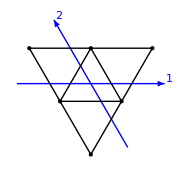

```mathematica
PlotRep2D[rep2, SimpleRoots]
```

Now let us multiply the two representations and look at the weight diagram of the product:

```mathematica
prodrep=RepProduct[rep1, rep2];
```

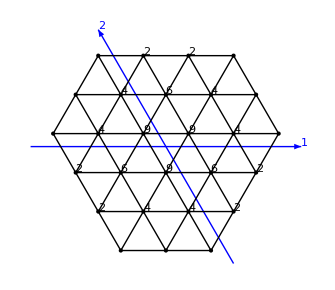

```mathematica
PlotRep2D[prodrep, SimpleRoots]
```

The usual Clebsch-Gordan decomposition of products is also applicable in this algebra. Here is an example of multiplying the previously defined representations rep1 and rep2:

```mathematica
CGDecomposition[DynkinLabels[rep1], DynkinLabels[rep2]]
```

15 ⊗ 6 = 42 ⊕ 24 ⊕ 15 ⊕ 6 ⊕ 3

{{3,2},{1,3},{2,1},{0,2},{1,0}}

```mathematica
DecomposeRep[prodrep, SimpleRoots]
```

Sub-multiplet 1:  {3,2}  dim=42

Sub-multiplet 2:  {1,3}  dim=24

Sub-multiplet 3:  {2,1}  dim=15

Sub-multiplet 4:  {0,2}  dim=6

Sub-multiplet 5:  {1,0}  dim=3

Total number of sub-mupltiplets: 5

{{3,2},{1,3},{2,1},{0,2},{1,0}}

Let us reproduce the famous results from SU(3) algebra (Note that it displays 3 instead of ):

```mathematica
rep3=BuildRep[{1,0}];
rep4=BuildRep[{0,1}];
CGDecomposition[rep3, rep4];
CGDecomposition[rep3, rep3, rep3];
```

3 ⊗ 3 = 8 ⊕ 1

3 ⊗ 3 ⊗ 3 = 10 ⊕ 8 ⊕ 8 ⊕ 1

The Weyl vector for the algebra can be evaluated:

```mathematica
DynkinLabels[WeylVector]
```

{1,1}

## Lie Algebra SU(4)

Now we look at the SU(4) algebra and look at its representations. This allows us to view their 3-dimensional weight diagrams.

```mathematica
SetGroup[SU[4]]
```

Set group is  A(3)

Rank of the group = 3

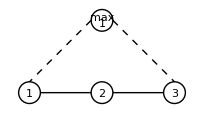

```mathematica
DynkinDiagram
```

```mathematica
CartanMatrix[SimpleRoots]//MatrixForm
```

(2 | -1 | 0
-1 | 2 | -1
0 | -1 | 2)

We can obtain the Coxeter plane of this algebra. It returns a pair of vectors that span the plane:

```mathematica
plane1=CoxeterPlane
```

{{0.5,-0.5,0.5,-0.5},{0.,0.707107,-0.707107,0.}}

We can again build a representation using its Dynkin labels and look at its weight diagram in 3D:

```mathematica
rep1=BuildRep[{0,1,0}, OutputMethod->"Weights"];
```

```mathematica
DynkinLabels[rep1]
```

{{{0,-1,0},1},{{-1,1,-1},1},{{1,0,-1},1},{{-1,0,1},1},{{1,-1,1},1},{{0,1,0},1}}

```mathematica
PlotRep3D[rep1, SimpleRoots]
```

-Graphics3D-

The PlotRep2D command can be used for this algebra to generate a projection of the weight diagram on a 2D plane - say, the Coxeter plane:

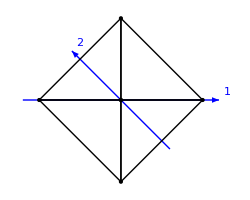

```mathematica
PlotRep2D[rep1, plane1]
```

The following command gives the dimension of the representation:

```mathematica
RepDimension[{0,1,0}]
```

6

```mathematica
rep2=BuildRep[{1,1,0}, OutputMethod->"Weights"];
```

```mathematica
DynkinLabels[rep2]
```

{{{0,-1,-1},1},{{-1,1,-2},1},{{1,0,-2},1},{{-1,0,0},2},{{1,-1,0},2},{{0,1,-1},2},{{0,-2,1},1},{{-2,2,-1},1},{{2,0,-1},1},{{-1,-1,2},1},{{1,-2,2},1},{{0,0,1},2},{{-2,1,1},1},{{2,-1,1},1},{{-1,2,0},1},{{1,1,0},1}}

```mathematica
PlotRep3D[rep2, SimpleRoots]
```

-Graphics3D-

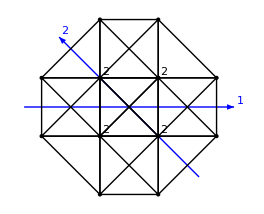

```mathematica
PlotRep2D[rep2, plane1]
```

```mathematica
prodrep=RepProduct[rep1, rep2];
```

```mathematica
DecomposeRep[prodrep, SimpleRoots]
```

Sub-multiplet 1:  {1,2,0}  dim=60

Sub-multiplet 2:  {2,0,1}  dim=36

Sub-multiplet 3:  {0,1,1}  dim=20

Sub-multiplet 4:  {1,0,0}  dim=4

Total number of sub-mupltiplets: 4

{{1,2,0},{2,0,1},{0,1,1},{1,0,0}}

## Dynkin Diagrams for other Lie Algebras

### or SO(11)

```mathematica
SetGroup[B[5]]
```

Set group is  B(5)

Rank of the group = 5

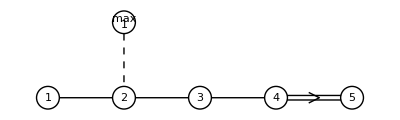

```mathematica
DynkinDiagram
```

### or Sp(10)

```mathematica
SetGroup[C[5]]
```

Set group is  C(5)

Rank of the group = 5

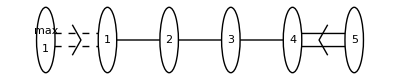

```mathematica
DynkinDiagram
```

### or SO(10)

```mathematica
SetGroup[D[5]]
```

Set group is  D(5)

Rank of the group = 5

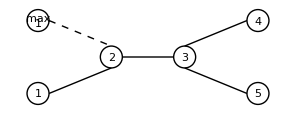

```mathematica
DynkinDiagram
```

```mathematica
SetGroup[G[2]]
```

Set group is  G(2)

Rank of the group = 2

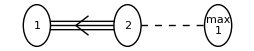

```mathematica
DynkinDiagram
```

```mathematica
SetGroup[F[4]]
```

Set group is  F(4)

Rank of the group = 4

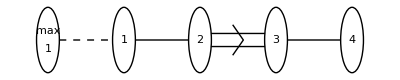

```mathematica
DynkinDiagram
```

```mathematica
SetGroup[E[6]]
```

Set group is  E(6)

Rank of the group = 6

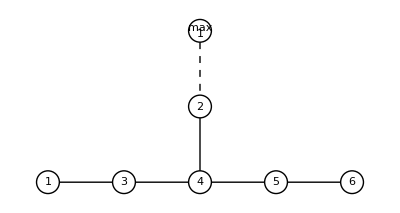

```mathematica
DynkinDiagram
```